#### Continuous system

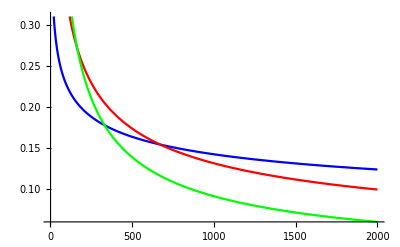

```mathematica
psi1[x_,σ_,e_]:=Re[ⅈ/(x^σ e (-ⅈ)^σ)Gamma[1+σ]];
psi2[x_,σ_,e_]:=Re[ⅈ/(x^(2*σ) e^2 (-ⅈ)^(2σ))Gamma[1+2σ]];
psi3[x_,σ_,e_]:=Re[ⅈ/(x^(3*σ) e^3 (-ⅈ)^(3σ))Gamma[1+3σ]];
Plot[{Abs@psi1[x,0.2,0.5],Abs@psi2[x,0.2,0.5],Abs@psi3[x,0.2,0.5]},{x,1,2000},PlotStyle->{Blue,Red,Green}]
```

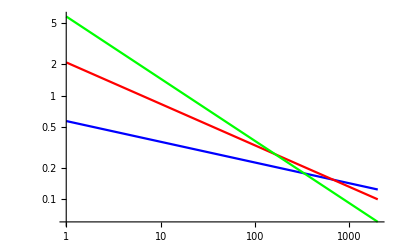

```mathematica
LogLogPlot[{Abs@psi1[x,0.2,0.5],Abs@psi2[x,0.2,0.5],Abs@psi3[x,0.2,0.5]},{x,1,2000},PlotStyle->{Blue,Red,Green}]
```

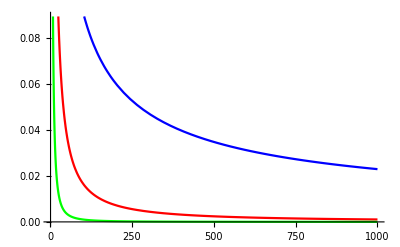

```mathematica
Plot[{Abs@psi1[x,0.6,0.5],Abs@psi2[x,0.6,0.5],Abs@psi3[x,0.6,0.5]},{x,1,1000},PlotStyle->{Blue,Red,Green}]
```

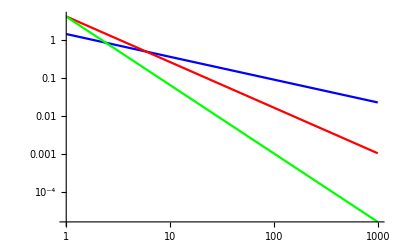

```mathematica
LogLogPlot[{Abs@psi1[x,0.6,0.5],Abs@psi2[x,0.6,0.5],Abs@psi3[x,0.6,0.5]},{x,1,1000},PlotStyle->{Blue,Red,Green}]
```

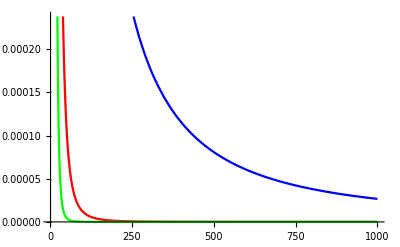

```mathematica
Plot[{Abs@psi1[x,1.6,0.5],Abs@psi2[x,1.6,0.5],Abs@psi3[x,1.6,0.5]},{x,1,1000},PlotStyle->{Blue,Red,Green}]
```

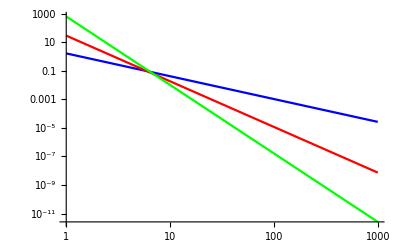

```mathematica
LogLogPlot[{Abs@psi1[x,1.6,0.5],Abs@psi2[x,1.6,0.5],Abs@psi3[x,1.6,0.5]},{x,1,1000},PlotStyle->{Blue,Red,Green}]
```

#### Discrete system: a=π case

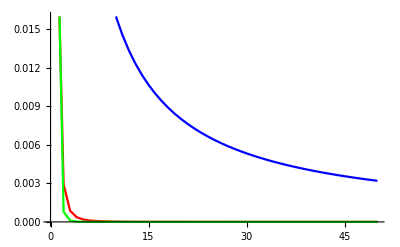

```mathematica
f1[x_,σ_,e_]:=-σ/(x^σ e)(π x)^(σ-1) Cos[π x]; 
f2[x_,σ_,e_]:=-σ/(x^σ e)(σ-1)(σ-2)(π x)^(σ-3) Cos[π x];
f3[x_,σ_,e_]:=-σ/(x^σ e)(σ-1)(σ-2)(σ-3)(σ-4)(π x)^(σ-5) Cos[π x];
ListLinePlot[{Table[Abs@f1[x,0.2,0.5],{x,1,50}],Table[Abs@f2[x,0.2,0.5],{x,1,50}],Table[Abs@f3[x,0.2,0.5],{x,1,50}]},PlotStyle->{Blue,Red,Green}]
```

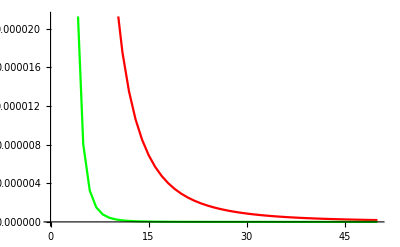

```mathematica
ListLinePlot[{Table[Abs@f2[x,0.2,0.5],{x,1,50}],Table[Abs@f3[x,0.2,0.5],{x,1,50}]},PlotStyle->{Red,Green}]
```

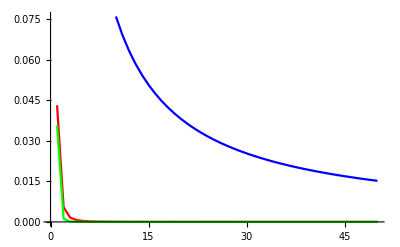

```mathematica
ListLinePlot[{Table[Abs@f1[x,0.6,0.5],{x,1,50}],Table[Abs@f2[x,0.6,0.5],{x,1,50}],Table[Abs@f3[x,0.6,0.5],{x,1,50}]},PlotStyle->{Blue,Red,Green}]
```

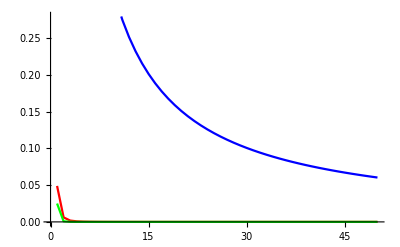

```mathematica
ListLinePlot[{Table[Abs@f1[x,1.2,0.5],{x,1,50}],Table[Abs@f2[x,1.2,0.5],{x,1,50}],Table[Abs@f3[x,1.2,0.5],{x,1,50}]},PlotStyle->{Blue,Red,Green}]
```

#### Discrete system: a=π/2 (reduced Brillouin zone) case

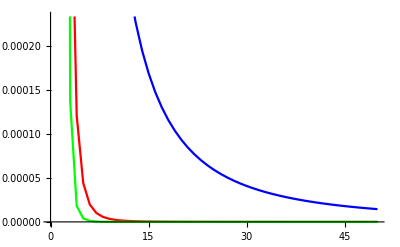

```mathematica
g1[x_,σ_,e_]:=σ/(x^σ e)(σ-1)((π x)/2)^(σ-2)Sin[π/2 x];
g2[x_,σ_,e_]:=σ/(x^σ e)(σ-1)(σ-2)(σ-3)((π x)/2)^(σ-4)Sin[π/2 x];
g3[x_,σ_,e_]:=σ/(x^σ e)(σ-1)(σ-2)(σ-3)(σ-4)(σ-5)((π x)/2)^(σ-6)Sin[π/2 x];
ListLinePlot[{Table[Abs@g1[x,0.2,0.5],{x,1,100,2}],Table[Abs@g2[x,0.2,0.5],{x,1,100,2}],Table[Abs@g3[x,0.2,0.5],{x,1,100,2}]},PlotStyle->{Blue,Red,Green}]
```

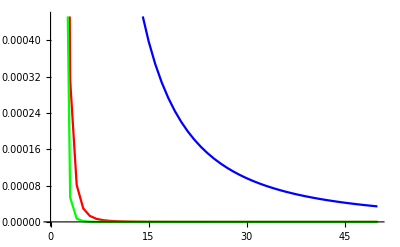

```mathematica
g1[x_,σ_,e_]:=σ/(x^σ e)(σ-1)((π x)/2)^(σ-2)Sin[π/2 x];
g2[x_,σ_,e_]:=σ/(x^σ e)(σ-1)(σ-2)(σ-3)((π x)/2)^(σ-4)Sin[π/2 x];
g3[x_,σ_,e_]:=σ/(x^σ e)(σ-1)(σ-2)(σ-3)(σ-4)(σ-5)((π x)/2)^(σ-6)Sin[π/2 x];
ListLinePlot[{Table[Abs@g1[x,1.2,0.5],{x,1,100,2}],Table[Abs@g2[x,1.2,0.5],{x,1,100,2}],Table[Abs@g3[x,1.2,0.5],{x,1,100,2}]},PlotStyle->{Blue,Red,Green}]
```